5

5

4

4

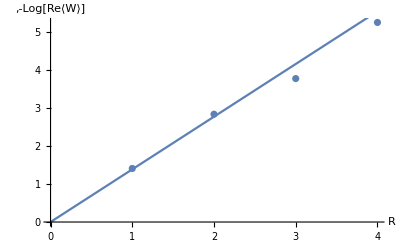

```mathematica
(*Lattice side Length*)
L=5;


(*Multiplication/Inverse Rule for Group SU2*)

AngleBracket[a1_,a2_]:=Flatten[{a1[[1]]*a2[[1]]-a1[[2;;4]].a2[[2;;4]],a1[[1]]*a2[[2;;4]]+a2[[1]]*a1[[2;;4]]-Cross[a1[[2;;4]],a2[[2;;4]]]}];
Conj[a1_]:=Flatten[{a1[[1]],-a1[[2;;4]]}];




wilsonlink[β_,R_,T_]:=Module[ {F1,F2,act1,act2,link1,link2,list1,list2,r,u,g,f,J,ϵ,q},

(*Initial lattice config.*)
F1=Table[{1,0,0,0},{i,L},{j,L},{k,L},{l,L},{m,4}];
F2=Table[RandomPoint[Sphere[{0,0,0,0}]],{i,L},{j,L},{k,L},{l,L},{m,4}];

(*Wilson Loop 1x1 Action *)
link1[F_,i_,j_,k_,l_,d1_,d2_]:=Module[{del,delx},
del[n_,m_,o_,p_]:=Part[F,Mod[i+n,L,1],Mod[j+m,L,1],Mod[k+o,L,1],Mod[l+p,L,1]];
delx[d_]:=del@@ReplacePart[{0,0,0,0},d->1];
Fold[⟨#1,#2⟩&,{del[0,0,0,0][[d1]],delx[d1][[d2]],delx[d2][[d1]]//Conj ,del[0,0,0,0][[d2]]//Conj}]
];

act1[F_]:=Module[{av},
av[i1_,j1_,k1_,l1_]:=link1[F,i1,j1,k1,l1,#1,#2]&@@@Subsets[{1,2,3,4},{2}]//Total;

1-(Sum[av[i,j,k,l][[1]],{i,L},{j,L},{k,L},{l,L}]/(6*(L^4)))
];

(*R by T Loop Expectation*)

link2[F_,i_,j_,k_,l_,d1_,d2_,R0_,T0_]:=Module[{del,delx,delx2},
del[n_,m_,o_,p_]:=Part[F,Mod[i+n,L,1],Mod[j+m,L,1],Mod[k+o,L,1],Mod[l+p,L,1]];
delx[d_,x_]:=del@@ReplacePart[{0,0,0,0},d->x];
delx2[v_,w_,x_,y_]:=del@@ReplacePart[{0,0,0,0},{v->x,w->y}];

Fold[⟨#1,#2⟩&,Join[
Table[delx[d1,v][[d1]],{v,0,T0-1}],
Table[delx2[d1,d2,T0,v][[d2]],{v,0,R0-1}],
Table[delx2[d1,d2,T0-v,R0][[d1]]//Conj,{v,1,T0}],
Table[delx[d2,R0-v][[d2]]//Conj,{v,1,R0}]

]]
];

act2[F_]:=Module[{av},
av[i1_,j1_,k1_,l1_]:=link2[F,i1,j1,k1,l1,#1,#2,R,T]&@@@Subsets[{1,2,3,4},{2}]//Total;


(Sum[av[i,j,k,l][[1]],{i,L},{j,L},{k,L},{l,L}]/(6*(L^4)))

];


(*Energy Density Data*)

list1=List[act1[F1]];
list2=List[act1[F2]];

(*"Monte Carlo" Rejection Sampling*)

r[t_]:=Module[{o},While[True,o=RandomReal[{Exp[-t*β],Exp[t*β]}];
If[RandomReal[]<Sqrt[1-(Log[o]/(β*t))^2],Break[]];];
Return[Log[o]/(β*t)]
];

(*Neighbouring plaquettes*)

u[F_,i_,j_,k_,l_,d_]:=Module[{del,delx,delx2,loop},

del[n_,m_,o_,p_]:=Part[F,Mod[i+n,L,1],Mod[j+m,L,1],Mod[k+o,L,1],Mod[l+p,L,1]];
delx[v_,x_]:=del@@ReplacePart[{0,0,0,0},v->x];
delx2[v_,w_,x_,y_]:=del@@ReplacePart[{0,0,0,0},{v->x,w->y}];

loop[s_]:=Fold[⟨#1,#2⟩&,{delx[d,1][[s]],delx[s,1][[d]]//Conj ,del[0,0,0,0][[s]]//Conj}]+Fold[⟨#1,#2⟩&,{delx2[s,d,-1,1][[s]]//Conj,delx[s,-1][[d]]//Conj ,delx[s,-1][[s]]}];

loop/@Cases[{1,2,3,4},Except[d]]//Total

];


(*Generating Rule*)

g[F_,i_,j_,k_,l_,d_]:=Module[{a0,a1,u0},
u0=u[F,i,j,k,l,d];
a0=r[Norm[u0]];
a1=RandomPoint[Sphere[{0,0,0},Sqrt[(1-a0^2)]]];
⟨Flatten[{a0,a1}],(u0/Norm[u0])//Conj⟩

];
 
(*Sweep Lattice*)
f[m_]:=Module[{s,i,j,k,l,d},
s=m;
For[i=1,i<L+1,i++,
For[j=1,j<L+1,j++,
For[k=1,k<L+1,k++,
For[l=1,l<L+1,l++,
For[d=1,d<4+1,d++,
s[[i,j,k,l,d]]=g[s,i,j,k,l,d];
];
];
];
];
];
s
];



(*Run Algorithm Max J Times*)
J=70;
ϵ=0.01;
For[q=1,q<J,q++,
F1=f[F1];
list1=Append[list1,act1[F1]];
F2=f[F2];
list2=Append[list2,act1[F2]];
If[Abs[(list1[[-1]]-list2[[-1]])/(list1[[-1]]+list2[[-1]])]<ϵ&&Abs[(list1[[-1]]-list1[[-2]])/(list1[[-1]]+list1[[-2]])]<ϵ&&Abs[(list2[[-1]]-list2[[-2]])/(list2[[-1]]+list2[[-2]])]<ϵ,Break[]]
];
Print[Length[list1]];
(act2[F1]+act2[F2])/2
];
β=1;
range=4;
data1=Table[{T0,-Log[wilsonlink[β,T0,1]]},{T0,1,range}];
Show[ListPlot[data1,PlotRange->All,AxesOrigin->{0,0}],Plot[-x Log[β/4],{x,0,4}], AxesStyle-> Thick, TicksStyle->Thick,LabelStyle->Directive[Black,Bold, Medium],AxesLabel->{"R",",-Log[Re⟨W⟩]"}]
```

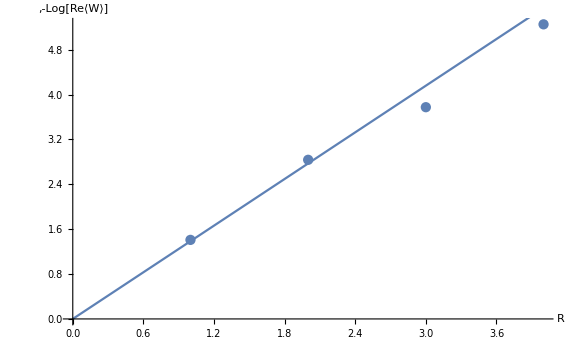

```mathematica
Show[%40,ImageSize->Large]
```

```mathematica
>
```

```mathematica
+
```